```mathematica
W[x_]:=x^(1-x) Exp[-0.531 (1-x)^2];
Wp[x_]:=(D[W[x0],x0])/.{x0->x};
R[x_]:=0.197 √(1/0.5482^2 Log[1/W[x]]);
fig3d=Show[Plot3D[None,{x,0,1},{y,-1,1},BoxRatios->{1,1,1},PlotRange->{{0,1},{-0.99,0.99},{-0.99,0.99}},Axes->True,AxesLabel->{Style["x",20],Style["a_y (fm)      ",20],Style["a_x (fm)  ",20]},LabelStyle->14,Ticks->All,Ticks->{{0,0.5,1},{-0.5,0,0.5},{-0.5,0,0.5}},ViewPoint->{0.7 Pi,-1.5 Pi,2.0}],
ParametricPlot3D[{{x,y,Sqrt[R[x]^2-y^2]},{x,y,-Sqrt[R[x]^2-y^2]}},{x,0.01,1},{y,-1,1},ColorFunction->Function[{x},Hue[x]],Mesh->14,MeshStyle->Opacity[0.4],PlotPoints->320,BoundaryStyle->{Opacity[0.7],Thickness[0.003]}]]
```

-Graphics3D-

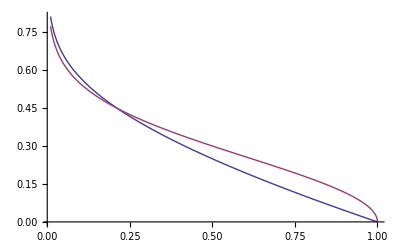

```mathematica
Plot[{R[x],0.197/0.5482 √Log[1/x]},{x,0.01,1}]
```

```mathematica
W[x_]:=x^(1-x) Exp[-0.531 (1-x)^2];
Wp[x_]:=(D[W[x0],x0])/.{x0->x};
HH[τ_,x_,b2_]:=(Gamma[τ-1/2]/(√π Gamma[τ-1])(1-W[x])^(τ-2) W[x]^(-1/2)Wp[x] λ/(π Log[1/W[x]]) Exp[(-λ b2/0.197^2)/Log[1/W[x]]])/.{λ->0.5482^2};
H[x_,b2_]:=(2-1.5/3) HH[3,x,b2]+1.5/3 HH[4,x,b2];
R[x_]:=0.197 √(1/0.5482^2 Log[1/W[x]]);
```

```mathematica
colorfunc[z_]:=Opacity[0.65,ColorData["TemperatureMap",z/1.3+(1-1/1.3)]];(*colorfunc[z_]:=Opacity[0.9,ColorData["Rainbow",z/1.4+(1-1/1.4)]];*)
```

```mathematica
slice3d=Show[ParametricPlot3D[{0.1,r Sin[θ],r Cos[θ]},{r,0,√2},{θ,-π/4,2π-π/4},BoxRatios->{1.5,1,1},PlotRange->{{0,1},{-0.99,0.99},{-0.99,0.99}},AxesLabel->{Style["x",20],Style["a_y(fm)      ",18],Style["a_x(fm)  ",18]},LabelStyle->14,ColorFunction->Function[{z,x,y},colorfunc[(H[0.1,x^2+y^2]-H[0.9,2])/H[0.1,0]]],ColorFunctionScaling->False,
Mesh->{{R[0.1]},{0,π/2,π,3 π/2}},MeshStyle->{{Thickness[0.003],Opacity[0.3]},{Thickness[0.001],Opacity[0.2]}},PlotPoints->30,BoundaryStyle->None],
(*ParametricPlot3D[{0.3,r Sin[θ],r Cos[θ]},{r,0,√2},{θ,-π/4,2π-π/4},ColorFunction->Function[{z,x,y},colorfunc[(H[0.3,x^2+y^2]-H[0.9,2])/H[0.1,0]]],ColorFunctionScaling->False,Mesh->{{R[0.3]},{0,π/2,π,3 π/2}},MeshStyle->{{Thickness[0.003],Opacity[0.3]},{Thickness[0.001],Opacity[0.2]}},PlotPoints->30,BoundaryStyle->None],*)
ParametricPlot3D[{0.4,r Sin[θ],r Cos[θ]},{r,0,√2},{θ,-π/4,2π-π/4},ColorFunction->Function[{z,x,y},colorfunc[(H[0.4,x^2+y^2]-H[0.9,2])/H[0.1,0]]],ColorFunctionScaling->False,Mesh->{{R[0.4]},{0,π/2,π,3 π/2}},MeshStyle->{{Thickness[0.003],Opacity[0.3]},{Thickness[0.001],Opacity[0.2]}},PlotPoints->30,BoundaryStyle->None],
(*ParametricPlot3D[{0.5,r Sin[θ],r Cos[θ]},{r,0,√2},{θ,-π/4,2π-π/4},ColorFunction->Function[{z,x,y},colorfunc[(H[0.5,x^2+y^2]-H[0.9,2])/H[0.1,0]]],ColorFunctionScaling->False,Mesh->{{R[0.5]},{0,π/2,π,3 π/2}},MeshStyle->{{Thickness[0.003],Opacity[0.3]},{Thickness[0.001],Opacity[0.2]}},PlotPoints->30,BoundaryStyle->None],*)
ParametricPlot3D[{0.7,r Sin[θ],r Cos[θ]},{r,0,√2},{θ,-π/4,2π-π/4},ColorFunction->Function[{z,x,y},colorfunc[(H[0.7,x^2+y^2]-H[0.9,2])/H[0.1,0]]],ColorFunctionScaling->False,Mesh->{{R[0.7]},{0,π/2,π,3 π/2}},MeshStyle->{{Thickness[0.003],Opacity[0.3]},{Thickness[0.001],Opacity[0.2]}},PlotPoints->30,BoundaryStyle->None],
(*ParametricPlot3D[{0.9,r Sin[θ],r Cos[θ]},{r,0,√2},{θ,-π/4,2π-π/4},ColorFunction->Function[{z,x,y},colorfunc[(H[0.9,x^2+y^2]-H[0.9,2])/H[0.1,0]]],ColorFunctionScaling->False,Mesh->{{R[0.9]},{0,π/2,π,3 π/2}},MeshStyle->{{Thickness[0.003],Opacity[0.3]},{Thickness[0.001],Opacity[0.2]}},PlotPoints->30,BoundaryStyle->None],*)
ParametricPlot3D[{x,R[x] Sin[θ],R[x] Cos[θ]},{x,0.01,1},{θ,0,3/2 π},ColorFunction->Function[{x},Opacity[0.6,Hue[x]]],Mesh->None,BoundaryStyle->None],
ParametricPlot3D[{x,0,R[x]},{x,0.01,1},ColorFunction->Function[{x},Opacity[0.6,Hue[x]] ],PlotStyle->Thickness[0.0055],Mesh->None,BoundaryStyle->None]
]
```

-Graphics3D-

```mathematica
Export["/Users/user/Liu/Repos/LFHQCD/notebook/slice3d-2.png",slice3d]
```

/Users/user/Liu/Repos/LFHQCD/notebook/slice3d-2.png